## Projection to dome

### initialize

```mathematica
ScreenAxes[n_,up_]:={Normalize[up-n up.n],Cross[Normalize[up-n up.n],n]}(*define two axes perpendicular to screen normal n, with the first toward the "up" direction*)
```

```mathematica
UnitSphereToEmbeddedScreen[v_,c_,FOV_]:=Cos[FOV/2]c+Cos[FOV/2](v/(v.c)-c);(*image is unit disk (S=1);c must be a unit vector*)
UnitSphereToScreen[v_,c_,I_,FOV_]:=Cot[FOV/2]I.(v/(v.c));(*image is unit disk (S=1);c must be a unit vector, I is projection matrix*)
```

```mathematica
ProjToScreen[t_,c_,I_,FOV_]:=UnitSphereToScreen[ProjectorToPerceptualSphere[t],c,I,FOV]
```

```mathematica
ProjectorToPerceptualSphere[t_]:=((*Module[{x,px,l,y,my,yz,L,z},*)
x=q+Sin[αt/2] t.{jx,jy};(*object position in physical space on screen plane*)
px=Normalize[x-p];(*unit vector through object position*)

l=-(p-m).px-√(((p-m).px)^2-Norm[p-m]^2+r^2);(*distance from projector to mirror*)
y=p+l px;(*point on mirror*)

my=Normalize[y-m];(*normal vector at incident ray target*)
yz=Normalize[2my(p-y).my-(p-y)];(*reflected ray*)

L=-(y-d).yz+√(((y-d).yz)^2-Norm[y-d]^2+R^2);(*distance from reflected ray to dome*)
z=y+L yz;(*object position on dome*)
Normalize[z-a]
(*]*)
)
```

#### parameters

```mathematica
defaultProjectorParams=(
p={3,0,-1.1};(*projector source*)
m={1,0,-.8};(*mirror center*)
r=.3;(*mirror radius*)
d={.5,0,-.2};(*dome center*)
R=1.2;(*dome radius*)
a={.4,.1,.1};(*animal eye position*)(*once was {.4,.1,.1}*)
αt=π/180. 30;(*screen field of view (FOV [°])*)
X=Sin[αt/2];
q=p+Cos[αt/2]Normalize[m+{0,0,.27}-p];(*projector center target*)
{jy,jx}=ScreenAxes[Normalize[q-p],{0,0,1}];(*screen y-axis points toward z direction, orthogonal to projector direction; x-axis is orthogonal to both*)
)
```

```mathematica
defaultCameraParams=(
o={0,0,0};(*camera origin*)
c=ProjectorToPerceptualSphere[{0.,0.}];(*camera center target*)
αs=π/180. 120;(*field of view (full width)*)
W=Abs[Sin[αs/2]];
B=Abs[Cos[αs/2]];
b=B c;
{iy,ix}=ScreenAxes[c,{0.,0.,1.}];
)
```

```mathematica
defaultConeParams=(
mp=Normalize[m-p];
μ=2ArcSin[r/Norm[m-p]];
ρ=m-mp r Sin[μ/2];
P=√(Norm[m-p]^2-r^2)Sin[μ/2];
J=ScreenAxes[mp,{0,0,1}];(*screen axes relative to projector pointed right at cone (instead of to q)*)
)
```

### 3D projector geometry

```mathematica
t={.04,-.08};
v=ProjectorToPerceptualSphere[t];
w=UnitSphereToEmbeddedScreen[v,c,αs];
Graphics3D[
{
Thick,
Green,Point[q],Point[p],Line[{p,x}],Line[{p,y}],Line[{p,p+Normalize[q-p]}],
Point[q],
Cyan,Line[{q-X jx,q+X jx}],
Magenta,Line[{q-X jy,q+X jy}],
Black,Point[x],
Black,Point[y],
Red,Point[m],Line[{m,y+my}],Arrow[{y,z}],{Opacity[.2],Sphere[m,r]},
Black,{Opacity[.1],Sphere[d,R]},Point[d],
Point[z],
Blue,Point[a],Arrow[{z,a}],
Blue,{Opacity[.1],Sphere[a]},
{Opacity[.2],Translate[Rotate[Polygon[Table[{W Cos[θ],W Sin[θ],B},{θ,0,2π,π/20}]],{{0,0,1},c}],a]},
Point[a+c],Line[{a,a+b}],
Black,Point[a+b],Arrow[{a+b,a+w}]
}
]
```

-Graphics3D-

### manipulate in 3D

```mathematica
Manipulate[
v=ProjectorToPerceptualSphere[-t];
w=UnitSphereToEmbeddedScreen[v,c,αs];
Graphics3D[
{
Thick,
Green,Point[q],Point[p],Line[{p,x}],Line[{p,y}],Line[{p,p+Normalize[q-p]}],
Point[q],
Cyan,Line[{q-X jx,q+X jx}],
Magenta,Line[{q-X jy,q+X jy}],
Black,Point[x],
Black,Point[y],
Red,Point[m],Line[{m,y+my}],Arrow[{y,z}],{Opacity[.2],Sphere[m,r]},
Black,{Opacity[.1],Sphere[d,R]},Point[d],
Point[z],
Blue,Point[a],Arrow[{z,a}],
Blue,{Opacity[.1],Sphere[a]},
{Opacity[.2],Translate[Rotate[Polygon[Table[{W Cos[θ],W Sin[θ],B},{θ,0,2π,π/20}]],{{0,0,1},c}],a]},
Point[a+c],Line[{a,a+b}],
Black,Point[a+b],Arrow[{a+b,a+w}]
}
]
,{{t,{0,0}},.2{-1,-1},.2{1,1}}]
```

### grid morphing screen→screen

#### cartesian

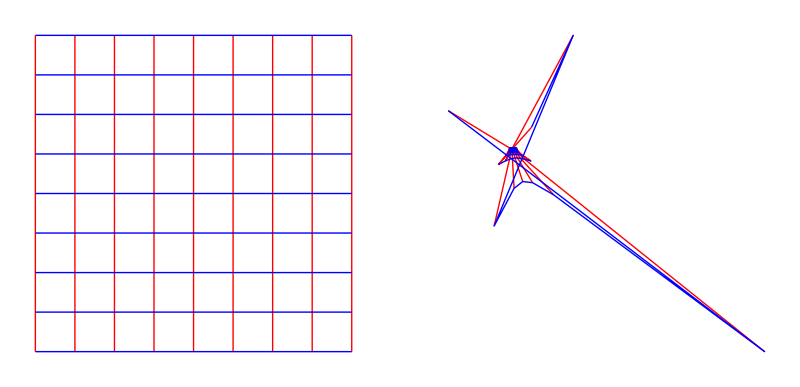

```mathematica
iL=jL=Range[-.2,.2,.05];
tLx=Table[{i,j},{i,iL},{j,jL}];
tLy=tLxᵀ;
sLx=Map[ProjToScreen[#,c,{ix,iy},αs/2]&,tLx,{2}];
sLy=sLxᵀ;
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy}],
Graphics[{Red,Line/@sLx,Blue,Line/@sLy},PlotRange->2]
}]
```

#### polar

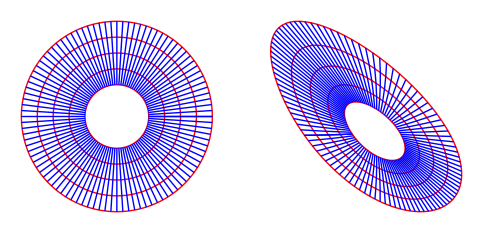

```mathematica
rL=Range[.01,.03,.005];
θL=Range[0,2π,π/50];
tLx=Table[r{Cos[θ],Sin[θ]},{r,rL},{θ,θL}];
tLy=tLxᵀ;
sLx=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLx,{2}];
sLy=sLxᵀ;
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy}],
Graphics[{Red,Line/@sLx,Blue,Line/@sLy},PlotRange->All]
}]
```

### spherical mapping of projector screen points

#### cartesian

```mathematica
dtx=.03;dty=.03;
ProjectorToPercept=Table[
ProjectorToPerceptualSphere[{tx,ty}]
,{tx,-1,1,dtx},{ty,-1,1,dty}];
```

```mathematica
Graphics3D[{
Blue,Table[Line[Select[ProjectorToPercept⟦ii⟧,(Im[Total[#]]==0)&]],{ii,Length[ProjectorToPercept]}],
Red,Table[Line[Select[ProjectorToPercept⟦All,jj⟧,(Im[Total[#]]==0)&]],{jj,Length[ProjectorToPerceptᵀ]}],
Glow[White],Black,Opacity[.8],Ball[{0,0,0},.95]
},
Lighting->None,Boxed->False
]
```

-Graphics3D-

#### polar

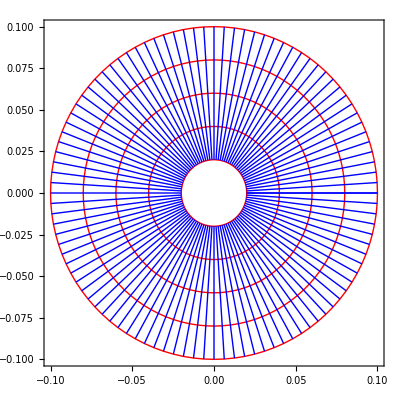

```mathematica
rL=Range[.02,.1,.02];
θL=Range[0,2π,π/50];
tLx=Table[r{Cos[θ],Sin[θ]},{r,rL},{θ,θL}];
tLy=tLxᵀ;
sLx=Map[ProjectorToPerceptualSphere,tLx,{2}];
sLy=sLxᵀ;
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy},Frame->True],
Graphics3D[{Red,Line/@sLx,Blue,Line/@sLy,Yellow,Opacity[.1],Sphere[]},PlotRange->1]
}]
```

### Allowable circle image

As long as the mirror is inside the dome, all rays from the mirror will hit the dome.
But there is only a cone of rays from the projector that will hit the mirror (since it is necessarily outside the mirror).
We can parameterize the screen patch that will hit the mirror best in terms of their spherical unit vectors, as this is described by a circle. Then map this circle to the screen, and this parameterizes the allowable rays.

```mathematica
Show[
Graphics3D[{
Thick,
Red,Point[m],{Opacity[.2],Sphere[m,r]},
Green,Point[p],Line[{p,m}],
Black,Line[{p,p+Norm[m-p]Normalize[q-p]}],
{Opacity[.2],Translate[Rotate[Polygon[Table[{P Cos[θ],P Sin[θ],0},{θ,0,2π,π/20}]],{{0,0,1},mp}],ρ]}
}],
ParametricPlot3D[ρ+P {Cos[θ],Sin[θ]}.J,{θ,0,π},PlotStyle->Cyan]
]
```

-Graphics3D-

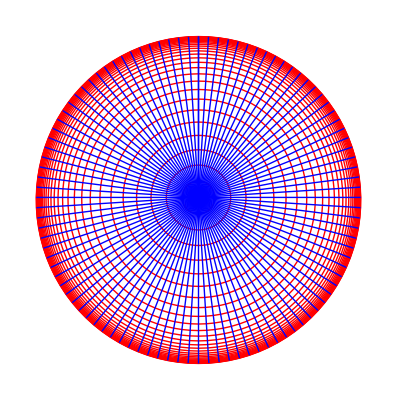

```mathematica
rrL=Tanh[3Range[0.,.99999,.033333]];
θL=Range[0,2π,π/50];
tLx=Table[UnitSphereToScreen[Normalize[ρ-p+rr P {Cos[θ],Sin[θ]}.J],Normalize[q-p],{jx,jy},αt],{rr,rrL},{θ,θL}];
tLy=tLxᵀ;
sLx=Map[ProjectorToPerceptualSphere,tLx,{2}];
sLy=sLxᵀ;
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy}],
Graphics3D[{Red,Line/@sLx,Blue,Line/@sLy,Yellow,Opacity[.1],Sphere[]},PlotRange->1]
}]
```

This is not the allowed projection: I need to project the mirror disk onto the SOURCE (left) image, and that will not be a circle! Then I can project that forward to the perceptual sphere.

### polar on cone, parametric on screen

#### Show full cone projection

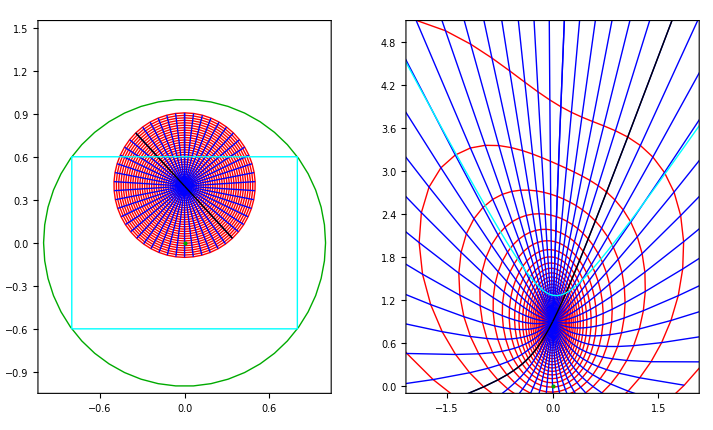

```mathematica
rrL=.89Range[0.,.99999,.033333];
uL=.99Range[-1,1,.01];
θL=Range[0,2π,2*π/50];
tLx=Table[UnitSphereToScreen[Normalize[ρ-p+rr P {Cos[θ],Sin[θ]}.J],Normalize[q-p],{jx,jy},αt],{rr,rrL},{θ,θL}];
tLy=tLxᵀ;
sLx=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLx,{2}];
sLy=sLxᵀ;
qL=Table[UnitSphereToScreen[
Normalize[q-p+X {Cos[θ],Sin[θ]}.{jx,jy}],Normalize[q-p],{jx,jy},αt],{θ,θL}];
qqL=Select[Map[ProjToScreen[#,c,{ix,iy},αs]&,qL,{1}],Im[Total[#]]==0&];
uuL=Table[UnitSphereToScreen[
Normalize[q-p+X {.8u,.6}.{jx,jy}],Normalize[q-p],{jx,jy},αt],{u,uL}];
uuuL=Select[Map[ProjToScreen[#,c,{ix,iy},αs]&,uuL,{1}],Im[Total[#]]==0&];
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy,
Thick,Black,Line/@tLy⟦{20,45}⟧,
Darker[Green],Line[qL],Point[{0,0}],
Cyan,Line[{{-.8,-.6},{.8,-.6},{.8,.6},{-.8,.6},{-.8,-.6}}]},Frame->True,PlotRange->{{-1,1},{-1.,1.5}}],
Graphics[{Red,Line/@sLx,Blue,Line/@sLy,
Thick,Black,Line/@sLy⟦{20,45}⟧,
Thick,Darker[Green],Line[Select[qqL,Positive[#⟦2⟧]&]],Point[{0,0}],
Cyan,Line[Select[uuuL,Positive[#⟦2⟧]&]]
},Frame->True,PlotRange->{{-2,2},{0,5}}]
}]
```

#### Show only on-screen parts that hit mirror

At some point the apparently allowed pixel falls off the mirror, at a radius ≈ .9187598*P off the ρ-p axis.
NO! The point is on the dome but outside of the perceptual field of view (even outside of the 180° field, which is why it switches sign).
One can only do the mapping on the image that remains in the field of view. Thus the distortion map should be defined for points where the source and the target both remain in the FOV.

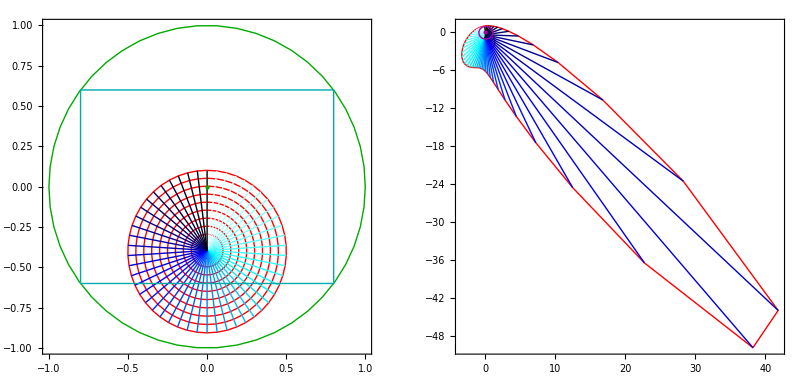

```mathematica
rrmax=.89;
rrL=Range[0,rrmax,rrmax/10];
uL=rrmax Range[-1,1,.01];(*rectangular screen*)
θL=Range[0,2π,2*π/50];
tLx=Table[UnitSphereToScreen[Normalize[ρ-p+rr P {Cos[θ],Sin[θ]}.J],Normalize[q-p],{jx,jy},αt],{rr,rrL},{θ,θL}];(*circles projected from p centered on mirror, mapped to projector screen which is not necessarily centered on mirror*)
tLy=Select[Norm[#]<1&]/@(tLxᵀ);(*select points within Field Of View of projector*)
tLx=Select[Norm[#]<1&]/@tLx;
sLx=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLx,{2}];(*map points to perceptual sphere*)
sLy=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLy,{2}];
qL=Table[UnitSphereToScreen[
Normalize[q-p+X {Cos[θ],Sin[θ]}.{jx,jy}],Normalize[q-p],{jx,jy},αt],{θ,θL}];(*edge of screen at FOV: maps to unit circle on screen!*)
qqL=Select[Map[ProjToScreen[#,c,{ix,iy},αs]&,qL,{1}],Im[Total[#]]==0&];
uuL=Table[UnitSphereToScreen[
Normalize[q-p+X {.8u,.6}.{jx,jy}],Normalize[q-p],{jx,jy},αt],{u,uL}];
uuuL=Select[Map[ProjToScreen[#,c,{ix,iy},αs]&,uuL,{1}],Im[Total[#]]==0&];
GraphicsRow[{
Graphics[{Red,Line/@tLx,{Blend[{White,Cyan,Blue,Black},#]&/@Range[0,1,1/(Length[tLy]-1)],Line/@tLy}ᵀ,
Thick,Darker[Green],Line[qL],Point[{0,0}],
Darker[Cyan],Line[{{-.8,-.6},{.8,-.6},{.8,.6},{-.8,.6},{-.8,-.6}}]},Frame->True,PlotRange->1],
Graphics[{Red,Line/@sLx,{Blend[{White,Cyan,Blue,Black},#]&/@Range[0,1,1/(Length[sLy]-1)],Line/@sLy}ᵀ,
Thick,Darker[Green],Line[Select[qqL,Norm[#]<1&]],
(*Darker[Cyan],Line[Select[uuuL,Norm[#]<10&]],*)
Darker[Magenta],Circle[{0,0},1],Point[{0,0}]
},Frame->True,PlotRange->1,PlotRangeClipping->True]
}]
```

Green is actual projector screen, which is distinct from the mirror-cone (red). The FOV of the perceptual screen is magenta.

## Inverse distortion map

### 2D

Define mesh points for the reverse interpolation function.
For the forward mapping, we compute how t maps to s, via s=f(h(t)).
For the inverse mapping, we use this same data in the reverse direction to determine how s maps to t, via t=g(s)=h^-1(f^-1(s)).
If we apply this inverse mapping, t=g(s), and then allow the mirror system to provide the forward mapping, s’=f(h(t)), then we obtain the map s’=f(h(g(s)))=s as desired.

```mathematica
rrmax=.96;
rrL=rrmax Tanh[2Range[0.,1.,1./30]]/Tanh[2];(*choose more points toward edge of mirror where distortion is greater*)

tL=Select[Norm[#]<1&][Union[Flatten[Table[UnitSphereToScreen[Normalize[ρ-p+rr P {Cos[θ],Sin[θ]}.J],Normalize[q-p],{jx,jy},αt],{rr,rrL},{θ,1000rr,2π+1000rr,2π/(100 rr^(1/2)+.01)}],1]]];(*choose angular sampling more densely at large rr*)

sL=Map[ProjToScreen[#,c,{ix,iy},αs]&,tL,{1}];(*map points to perceptual screen*)
tsL=Select[(Norm[#⟦2⟧]<1&&Im[Total[#⟦2⟧]]==0)&][{tL,sL}ᵀ]ᵀ;
```

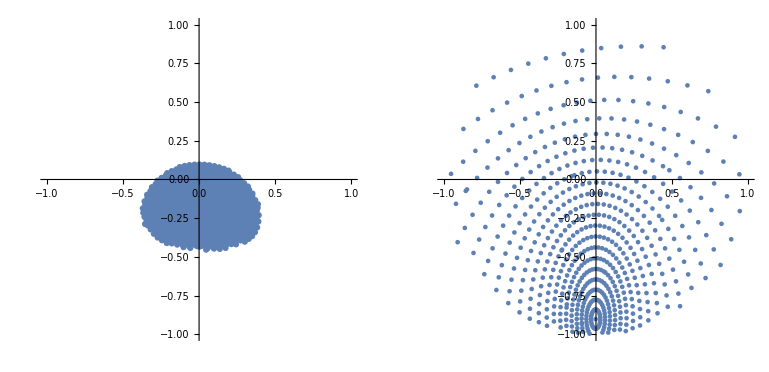

```mathematica
GraphicsRow[ListPlot[#,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]&/@tsL]
```

```mathematica
gx=Interpolation[{tsL⟦2⟧(*sx,sy*),tsL⟦1,All,1⟧(*tx*)}ᵀ,InterpolationOrder->1];
gy=Interpolation[{tsL⟦2⟧(*sx,sy*),tsL⟦1,All,2⟧(*ty*)}ᵀ,InterpolationOrder->1];
```

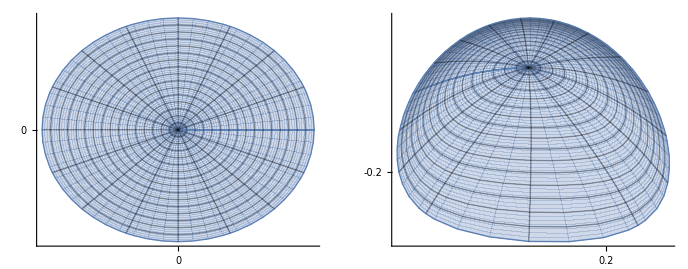

```mathematica
GraphicsRow[{
ParametricPlot[
{rr Cos[θ],rr Sin[θ]}
,{rr,0,.8},{θ,0,2π},Mesh->Automatic,Frame->False,Ticks->{Range[-1,1],Range[-1,1]}],
ParametricPlot[{
gx[rr Cos[θ],rr Sin[θ]],
gy[rr Cos[θ],rr Sin[θ]]
},{rr,0,.8},{θ,0,2π},Mesh->Automatic,Frame->False,Ticks->{Range[-1,1,.1],Range[-1,1,.1]}]}]
```

## Apply distortion map and project forward through mirrors

```mathematica
rrmax=.9;
rrL=Range[.001,rrmax,rrmax/10];
θL=Range[0,2π,2*π/50];
sLx=Table[rr{Cos[θ],Sin[θ]},{rr,rrL},{θ,θL}];
tLx=Transpose[{Apply[gx,sLx,{2}],Apply[gy,sLx,{2}]},{3,1,2}];
tLx=Select[Norm[#]<1&]/@tLx;
s2Lx=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLx,{2}];

sLy=Table[rr{Cos[θ],Sin[θ]},{rr,rrL},{θ,θL}]ᵀ;
tLy=Transpose[{Apply[gx,sLy,{2}],Apply[gy,sLy,{2}]},{3,1,2}];
tLy=Select[Norm[#]<1&]/@tLy;
s2Ly=Map[ProjToScreen[#,c,{ix,iy},αs]&,tLy,{2}];
```

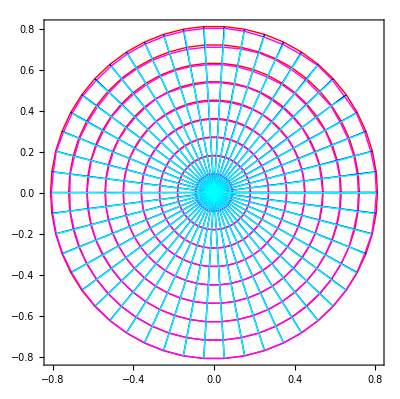

```mathematica
Graphics[{Red,Line/@sLx,Magenta,Line/@s2Lx,
Blue,Line/@sLy,Cyan,Line/@s2Ly
},Frame->True,PlotRange->1,PlotRangeClipping->True]
```

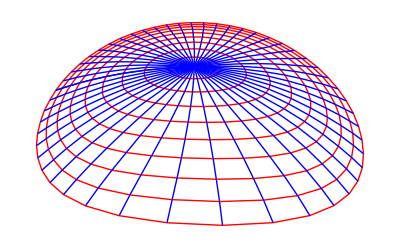

```mathematica
sLx=Map[ProjectorToPerceptualSphere,tLx,{2}];
sLy=Map[ProjectorToPerceptualSphere,tLy,{2}];
esLx=Map[UnitSphereToEmbeddedScreen[#,c,αs]&,sLx,{2}];
esLy=Map[UnitSphereToEmbeddedScreen[#,c,αs]&,sLy,{2}];(*perceptual screen embedded in physical space*)
GraphicsRow[{
Graphics[{Red,Line/@tLx,Blue,Line/@tLy}],
Graphics3D[{Red,Line/@sLx,Blue,Line/@sLy,Yellow,Opacity[.1],Sphere[]},PlotRange->1],
Graphics3D[{Red,Line/@esLx,Blue,Line/@esLy,Yellow,Opacity[.1],Sphere[]},PlotRange->1]
}]
```

```mathematica
t={0,0};
v=ProjectorToPerceptualSphere[t];
w=UnitSphereToEmbeddedScreen[v,c,αs];
etLx=Map[q+X #.{jx,jy}&,tLx,{2}];
etLy=Map[q+X #.{jx,jy}&,tLy,{2}];
projectionDiagram=Graphics3D[
{
Thickness[.002],
Red,Translate[Line/@sLx,a],Blue,Translate[Line/@sLy,a],
{Opacity[.5],Red,Translate[Line/@esLx,a],Blue,Translate[Line/@esLy,a]},
Red,Line/@etLx,Blue,Line/@etLy,
Thickness[.003],
Green,Point[q],Point[p],Line[{p,x}],Line[{p,y}],Line[{p,p+Normalize[q-p]}],
Point[q],
Cyan,Line[{q-X jx,q+X jx}],
Magenta,Line[{q-X jy,q+X jy}],
Black,Point[x],
Black,Point[y],
Red,Point[m],Arrow[{y,z}],{Opacity[.2],Sphere[m,r]},
Black,Line[{m,m+.5my}],
Black,{Opacity[.1],Sphere[d,R]},Point[d],
Point[z],
Blue,Point[a],Arrow[{z,a}],
Yellow,{Opacity[.1],Sphere[a]},
{Opacity[.2],Translate[Rotate[Polygon[Table[{W Cos[θ],W Sin[θ],B},{θ,0,2π,π/20}]],{{0,0,1},c}],a]},
Black,Point[a+b],Arrow[{a+b,a+w}]
},Boxed->False,ViewPoint->{-1.5,-3,1}
]
```

-Graphics3D-

```mathematica
Export["/Users/xaq/Projects/Fireflies/Figures/projectionDiagram.tif",projectionDiagram,ImageSize->4096]
```

/Users/xaq/Projects/Fireflies/Figures/projectionDiagram.tif

## Image transformations

```mathematica
ImageTransformation[img,ProjToScreen[{-0.,-.4}+#/200,c,{ix,iy},αs/2]&,100,DataRange->Full]
```

-Graphics-

```mathematica
img
```

-Graphics-

```mathematica
ρL=Range[.02,.2,.02];
dθ=π/50;
θL=Range[0,2π-dθ,dθ];
dataT=Flatten[Table[ρ{Cos[θ],Sin[θ]},{ρ,ρL},{θ,θL}],1];
dataS=Flatten[Table[ProjToScreen[ρ{Cos[θ],Sin[θ]},c,{ix,iy},αs/2],{ρ,ρL},{θ,θL}],1];
```

```mathematica
HinvR=Interpolation[Table[{dataS⟦i⟧,dataT⟦i,1⟧},{i,Length[dataS]}]];
Hinvθ=Interpolation[Table[{dataS⟦i⟧,dataT⟦i,2⟧},{i,Length[dataS]}]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

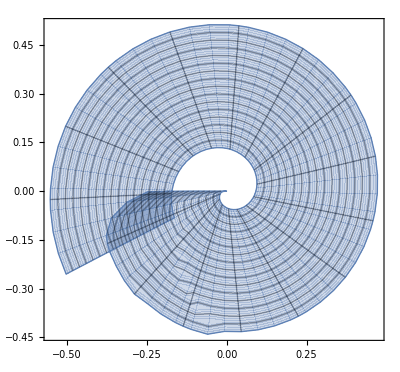

```mathematica
ParametricPlot[HinvR[ρ,θ]{Cos[#],Sin[#]}&[Hinvθ[ρ,θ]],{ρ,.002,1.},{θ,0,12π},Mesh->Automatic]
```